# Novel Minimal Universal Classical and Quantum Gates

## Theoretical approaches to representing discrete operators as linear state space transformations, a proof of classical universality, and a proposed smallest 2→2 universal quantum gate set.

## Introduction

### Universal Classical Gates

Classical logic uses logical operators, called gates, that transform one or more boolean-valued inputs to one or more boolean-valued outputs. For example, the AND gate returns True only when both of it’s inputs are True. AND is of the form 2→1, because it takes in two inputs and returns a single output.
An operation of two boolean values can be represented by a truth table, with each axis representing each input.

#### Truth Table Implementation

```mathematica
(* For Boolean (True or False)-valued functions *)
truthTable[func_, inputName_:"_None"]:=Grid[
  (* Truth Table with Axis Labels *)
 {{If[inputName=="_None", If[StringContainsQ[ToString[func], "&"], "func&", func], inputName], "0", "1"},
  {"0", b2i@func[False, False], b2i@func[False, True]},
  {"1", b2i@func[True, False], b2i@func[True, True]}},
  
 (* Dividers to seperate inputs and outputs *)
 Dividers->{{2->True}, {2->True}},
 
 (* Alligns the input labels to the right *)
 Alignment->{Right, Baseline},
 
 (* Color based on the value of each cell *)
 Background->{None, None, Flatten@Table[
  {b1, b2}->If[
     func[i2b[b1-2], i2b[b2-2]],
     SetAlphaChannel[Green, 0.5],
     SetAlphaChannel[Red, 0.5]],
    {b2, {2, 3}},
    {b1, {2, 3}}]}]

(* For Integer Boolean (1 or 0)-valued functions *)
numericalTruthTable[func_, inputName_:"_None"]:=Grid[
  (* Truth Table with Axis Labels *)
 {{If[inputName=="_None", If[StringContainsQ[ToString[func],"&"], "func&", func], inputName], "0", "1"},
  {"0", func[0, 0], func[0, 1]},
  {"1", func[1, 0], func[1, 1]}},
  
 (* Dividers to seperate inputs and outputs *)
 Dividers->{{2->True}, {2->True}},
 
 (* Alligns the input labels to the right *)
 Alignment->{Right, Baseline},
 
 (* Color based on the value of each cell *)
 Background->{None, None, Flatten@Table[
  {b1, b2}->
   (func[b1-2, b2-2])SetAlphaChannel[Green, 0.5]+(1-func[b1-2, b2-2])SetAlphaChannel[Red, 0.5],
    {b2, {2, 3}},
    {b1, {2, 3}}]}]
```

#### Example

```mathematica
truthTable[And]
```

And | 0 | 1
0 | 0 | 0
1 | 0 | 1

Some gates are able to be composed with themselves to make any other possible gate. These gates are called universal gate.
There are only two universal, classical, 2→1 gates, as will be proved later on: NAND (⊼) and NOR (⊽). For example, here is how the NAND gate can represent the XOR gate with a circuit diagram and code:
-Graphics-

```mathematica
(* XOR from NAND gates *)
xorFromNand[a_, b_]:=(((a⊼a)⊼(b⊼b))⊼(a⊼b))⊼(((a⊼a)⊼(b⊼b))⊼(a⊼b));

(* Display Truth Tables *)
Row[{truthTable[Xor, "Xor Built-In"], Spacer[10], truthTable[xorFromNand, "Xor from Nand"]}]
```

Xor Built-In | 0 | 1
0 | 0 | 1
1 | 1 | 0Xor from Nand | 0 | 1
0 | 0 | 1
1 | 1 | 0

Here is every gate represented with the built-in function, with only NANDs, and with only NORs:

```mathematica
and1[a_, b_]:=And[a, b];
and2[a_, b_]:=(a⊼b)⊼(a⊼b);
and3[a_, b_]:=(a⊽a)⊽(b⊽b);

or1[a_, b_]:=Or[a, b];
or2[a_, b_]:=(a⊼a)⊼(b⊼b);
or3[a_, b_]:=(a⊽b)⊽(a⊽b);

xor1[a_, b_]:=Xor[a, b];
xor2[a_, b_]:=(((a⊼a)⊼(b⊼b))⊼(a⊼b))⊼(((a⊼a)⊼(b⊼b))⊼(a⊼b));
xor3[a_, b_]:=(((a⊽b)⊽(a⊽b))⊽((a⊽b)⊽(a⊽b)))⊽((a⊽a)⊽(b⊽b));

nand1[a_, b_]:=Nand[a, b];
nand2[a_, b_]:=a⊼b;
nand3[a_, b_]:=((a⊽a)⊽(b⊽b))⊽((a⊽a)⊽(b⊽b));

nor1[a_, b_]:=Nor[a, b];
nor2[a_, b_]:=((a⊼a)⊼(b⊼b))⊼((a⊼a)⊼(b⊼b));
nor3[a_, b_]:=a⊽b;

xnor1[a_, b_]:=Xnor[a, b];
xnor2[a_, b_]:=(((a⊼a)⊼(b⊼b))⊼(a⊼b));
xnor3[a_, b_]:=((((a⊽b)⊽(a⊽b))⊽((a⊽b)⊽(a⊽b)))⊽((a⊽a)⊽(b⊽b)))⊽((((a⊽b)⊽(a⊽b))⊽((a⊽b)⊽(a⊽b)))⊽((a⊽a)⊽(b⊽b)))


Grid[
Transpose@(truthTable[#]&/@#&/@{{and1, and2, and3}, {or1, or2, or3}, {xor1, xor2, xor3}, {nand1, nand2, nand3}, {nor1, nor2, nor3}, {xnor1, xnor2, xnor3}}),
Spacings->{3, 2}]
```

and1 | 0 | 1
0 | 0 | 0
1 | 0 | 1 | or1 | 0 | 1
0 | 0 | 1
1 | 1 | 1 | xor1 | 0 | 1
0 | 0 | 1
1 | 1 | 0 | nand1 | 0 | 1
0 | 1 | 1
1 | 1 | 0 | nor1 | 0 | 1
0 | 1 | 0
1 | 0 | 0 | xnor1 | 0 | 1
0 | 1 | 0
1 | 0 | 1
and2 | 0 | 1
0 | 0 | 0
1 | 0 | 1 | or2 | 0 | 1
0 | 0 | 1
1 | 1 | 1 | xor2 | 0 | 1
0 | 0 | 1
1 | 1 | 0 | nand2 | 0 | 1
0 | 1 | 1
1 | 1 | 0 | nor2 | 0 | 1
0 | 1 | 0
1 | 0 | 0 | xnor2 | 0 | 1
0 | 1 | 0
1 | 0 | 1
and3 | 0 | 1
0 | 0 | 0
1 | 0 | 1 | or3 | 0 | 1
0 | 0 | 1
1 | 1 | 1 | xor3 | 0 | 1
0 | 0 | 1
1 | 1 | 0 | nand3 | 0 | 1
0 | 1 | 1
1 | 1 | 0 | nor3 | 0 | 1
0 | 1 | 0
1 | 0 | 0 | xnor3 | 0 | 1
0 | 1 | 0
1 | 0 | 1

### State Vector Representation of Operations

Classical 2→1 gates are usually considered to be a function with two inputs and one output. However, there is an alternative interpretation of gates as a linear operation on a unit basis vector representing the systems total state. This allows for all operations to be represented as matrix multiplications, and generalizes easily to quantum circuits.

#### State Vector

Let   𝔹   be   the   set   of   binary   numbers   {0, 1} .

An n-bit system can be represented with a vector in 𝔹^n, such that each dimension of the vector corresponds to a bit in the state. A gate can be considered to be an association of each input state—of the  total  possible states—to a specific output state.
A vector can be constructed in 𝔹^(2^n) so that each dimension corresponds to a possible state. Thus, a unit basis vector of 𝔹^(2^n) represents one singular state. A matrix transforms the ith basis vector e_i to the ith column in the matrix V_i.

For example, in the 4-bit binary system 1011, there are  possible states, so the 16-dimensional state vector representing this system is [0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0].
Note that the state vector of the binary number n (11 in this example) is the basis vector e_n, assuming the vector is indexed from 0.

#### Gate Application to a State Vector

A matrix M = [V_0 | V_1 | V_2 | V_3 | V_4 | V_5 | V_6 | V_7 | V_8 | V_9 | V_10 | V_11 | V_12 | V_13 | V_14 | V_15], where V_i∈𝔹^(2^n), takes the ith basis vector to V_i (i.e., M\[Application]e_i=V_i).
This means that M can associate each basis vector e_i to a specific output vector V_i, so, by our definition of a gate operation, this matrix can apply any arbitrary gate.

#### Motivation

The reason for representing gates as matrix multiplication is two-fold:
Firstly, in this representation, all gates are linear transformations, which can be easily composed and reasoned about. A whole circuit, made up of many gate operations, can be simplified to just a single matrix. Thus, the problem of determining whether a set of gates is universal is equivalent to the problem of whether every gate matrix can be decomposed into a product of elements in that set.
Secondly, quantum systems exhibit phenomena such as superposition and entanglement, in which a quantum state may be in a linear combination of multiple states at the same time, and in which a full state can not be represented as the tensor product of individual qubit states, respectively. This means that an n-bit quantum state can be represented by a vector on the complex unit hypersphere of ℂ^(2^n). The reason it must be on the unit hypersphere is because the magnitude of the vector must be equal to one, which is equivalent to the statement that the sum of the probabilities of the states of a random system is one.

### Universal Quantum Gate Sets

Universal quantum gates should be able to recreate any possible other quantum gate. However, due to the fact that quantum state vectors are complex, there is a continuous space of possible gates, which cannot be described exactly by a finite universal set. For example, the arbitrary Z rotation gate (ⅇ^(-ⅈ θ/2) | 0
0 | ⅇ^(ⅈ θ/2)) is a valid quantum gate for any choice of θ.
Instead, a universal quantum gate set is defined as one which can approximate any quantum gate to within some error factor ε. Formally, in order to represent a target gate T in terms of the finite gate set S_G,
‖T-M_1 M_2... M_f‖<=ε where M_i∈S_G, for some appropriate matrix norm, such as the maximum L2 norm of the columns.

## Quantum Computer Simulator Implementation

In order to explore quantum logic gates and quantum circuits more effectively, I wrote a simulation of a quantum computer which can run any arbitrary quantum circuit, though it is of exponential complexity with respect to the number of wires, even for circuits which theoretically can be simulated efficiently.

### Boolean State Vectors

#### Booleans

Here are a variety of helper functions which convert between booleans (b), integers (i), and state vectors (v):

```mathematica
b2i[b_] := If[b, 1, 0]
b2i[b_List] := b2i/@b
i2b[b_Integer] := b==1;
i2b[b_List] := i2b/@b

b2v[b_] := If[b, {0, 1}, {1, 0}]
i2v[b_Integer] := If[b==1, {0, 1}, {1, 0}]
v2i[{v1_Integer, v2_Integer}] := v1*0+v2*1
```

#### Tensors and State Construction

A state containing multiple bits is constructed by taking the tensor product of each consecutive bit’s state. tensor takes the tensor product of vectors, and fullState constructs the state vector of a list of boolean values.

```mathematica
tensor[v__] := Flatten[TensorProduct[v]]
fullState[b_List] := tensor@@i2v/@b
```

### Matrix Definitions

Each matrix representing an operation has a different form. For example, the NOT matrix is {{0, 1}, {1, 0}}.
Some matrices are constant and worked out by hand beforehand.
Other matrix operations may need arguments, and so has to be computed. This is done by computing the desired output for each input, then representing the inputs and outputs as state vectors, then constructing the M matrix from each output V_i.

#### Constant Matrices

```mathematica
matrixNot = ({{0, 1}, {1, 0}});
matrixCopy = ({{1, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 1}}); (* Only possible in classical computation due to the No Cloning Theorem *)
matrixNand = ({{0, 0, 0, 0}, {1, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});
matrixNor = ({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 1, 1}, {0, 0, 0, 0}});
```

Here is a visualization of each of those matrices:

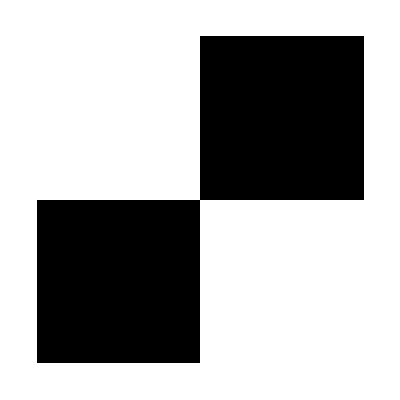
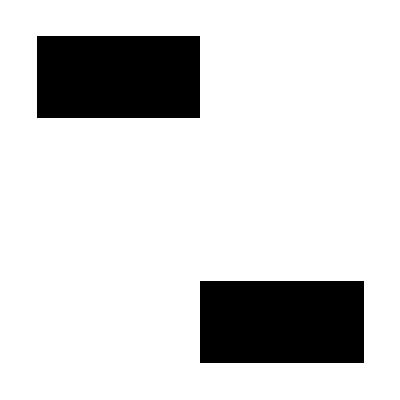
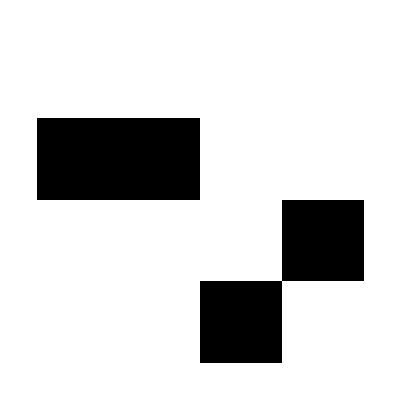
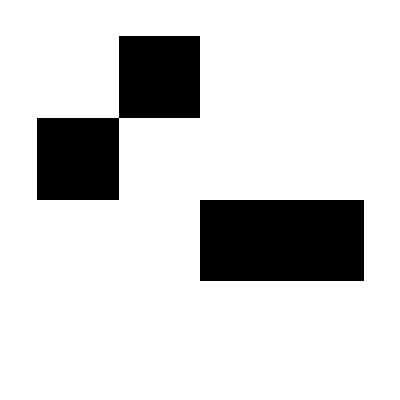

```mathematica
ArrayPlot/@{matrixNot, matrixCopy, matrixNand, matrixNor}
```

#### Computed Matrices

Swap switches two bits at positions s1 and s2.

```mathematica
(* Generates the ith column of SWAP *)
ViSwap[i_, n_, s1_, s2_] := Module[{bv, sbv},
 bv=IntegerDigits[i, 2, n];
 sbv=fullState[Table[bv[[Switch[j, s1, s2, s2, s1, _, j]]], {j,n}]]]

(* Generates SWAP column-wise *)
matrixSwap[n_, s1_, s2_]:=Table[ViSwap[i, n, s1, s2], {i, 0, 2^n-1}]
```

Return reduces the number of bits, thereby creating a smaller subset of the original bits to use as an output.

```mathematica
(* Generates the ith column of Return *)
ViReturn[i_, n_, s1_, s2_]:=tensor@@i2v/@(IntegerDigits[i, 2, n])[[Span[s1, s2]]]

(* Generates Return column-wise *)
matrixReturn[n_, s1_, s2_]:=Transpose[ViReturn[#, n, s1, s2]&/@Range[0, 2^n-1]]
```

For example, here is how a state vector of length 2^5=32 is reduced to a single bit state vector:

```mathematica
matrixReturn[5, 5, 5]//MatrixForm
```

(1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1)

Expand increases the number of bits, initializing the circuit to a particular state, either of the form
matrixZeroExpand[a, b] → │ab0000...⟩
or
matrixRepeatExpand[a, b] → │ababab...⟩.

```mathematica
matrixZeroExpand[n_, s1_, s2_]:=Module[{ω1, ω2, Ω1, Ω2},
 ω1=s1-1; Ω1=2^ω1; (* ω1 is the number of bits of the input, Ω1 is the size of the state vector of the input. *)
 ω2=s2; Ω2=2^ω2;   (* ω2 is the number of bits of the output, Ω2 is the size of the state vector of the output. *)
 Table[Module[{Vω1, Vω2, VΩ2},
  Vω1=IntegerDigits[i, 2, ω1];
  Vω2=Join[Vω1, ConstantArray[0, ω2-ω1]];
  VΩ2=fullState[Vω2];
  VΩ2], {i, 0, Ω1-1}]]//Transpose

matrixRepeatExpand[n_, s1_, s2_]:=Module[{ω1, ω2, Ω1, Ω2},
 ω1=s1-1; Ω1=2^ω1; (* ω1 is the number of bits of the input, Ω1 is the size of the state vector of the input. *)
 ω2=s2; Ω2=2^ω2;   (* ω2 is the number of bits of the output, Ω2 is the size of the state vector of the output. *)
 Table[Module[{Vω1, Vω2, VΩ2},
  Vω1=IntegerDigits[i, 2, ω1];
  Vω2=Flatten[ConstantArray[Vω1, ⌈ω2/ω1⌉]][[;;ω2]];
  VΩ2=fullState[Vω2];
  VΩ2], {i, 0, Ω1-1}]]//Transpose
```

For example, here are the expansion matrices increasing a systems wire count from 2 to 5

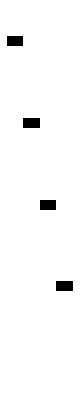
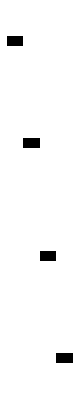

```mathematica
ArrayPlot/@{matrixZeroExpand[5, 3, 5], matrixRepeatExpand[5, 3, 5]}
```

### Gates to Matrices

In order to apply a 2-bit gate to a >2-bit system, the matrix cannot be multiplied directly with the state vector of the entire system. Rather, the gate matrix needs to be composed with Identity matrices representing the lack of operations on other bits. The computed matrices, because they are in a shape other than 2^2×2^2, are made in the correct dimension, so they are able to apply to the whole state. Here is how each gate is converted to a matrix:

```mathematica
matrixFormOfColumn[G_, n_] :=
  (* M = G[[2]] *)
  (* s1 = G[[1, 1]] *)
  (* s2 = G[[1, 2]] *)
  If[MatchQ[G[[2]], _List], (* For fixed matrices *)
   
    KroneckerProduct[IdentityMatrix[2^(G[[1,1]]-1)], G[[2]], IdentityMatrix[2^(n - G[[1, 2]])]],
   If[Length[G[[1]]]==3,
    G[[2]][G[[1,3]]], (* Arbitrary Rotation Gate *)
    G[[2]][n, G[[1, 1]], G[[1, 2]]]]] (* Computed matrix: uses Mtype[n, s1, s2] *)
```

For example, here is how the NAND gate is represented when applied to the last two bits of a 4-bit system. The repeating NAND pattern can be seen on the least significant bits, and the diagonal identity pattern can be seen on the most significant bits.

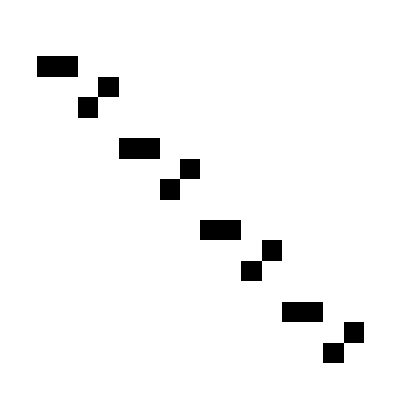

```mathematica
matrixFormOfColumn[{{3, 4}, matrixNand}, 4]//ArrayPlot
```

### Circuits Implementation

#### Circuit Application

A circuit is the composition of a set of gates applied to a set of wires. Because each gate is represented by a matrix, application of a gate is equivalent to multiplication of a state vector by a matrix. Because matrix multiplication is associative, all of the matrices of a circuit can be multiplied together into a single total circuit matrix. As most circuits require many more internal wires than input or output wires, a circuit matrix can be precomputed (which will take a relatively large amount of time) and then applied to one or more input state vectors (which will take a relatively small amount of time).
Finally, we can convert apply circuit to a logical function which can be displayed.
Here is the code that does this, first computing each matrix for each gate, then composing them by multiplication, then applying them to an input state, then creating a logic function from that:

```mathematica
(* Generates a matrix for each column of a circuit *)
circuitMatrices[circuit_] := With[{n = Max@Flatten@circuit[[All, 1, 1;;2]]}, matrixFormOfColumn[#, n]& /@ circuit];

(* Generates a combined matrix representing the whole circuit *)
circuitMatrix[circuit_] := Dot @@ Reverse @ circuitMatrices[circuit]

(* Apples the combined matrix to a state vector, returning an output state vector *)
applyCircuit[circuit_, state_] := circuitMatrix[circuit].state

(* Represents circuit application as a function in boolean logic *)
logicFunctionFromCircuit[circuit_] := v2i[circuitMatrix[circuit].fullState[{##}]]&  (* Only works for 2->2 logic gates *)
```

#### Circuit Visualization

Using the Wolfram Quantum Framework Paclet, my circuits can be converted into the paclet’s representation of a circuit, which can then be displayed. The paclet is also much more optimized, so I may use it’s code to more quickly compute matrix applications

```mathematica
PacletInstall["Wolfram/QuantumFramework"];

quantumOperatorFormOfColumn[i_Integer, gates_, n_]:=
Module[{G, s1, s2, M},
 G=gates[[i]];
 s1=G[[1, 1]];
 s2=G[[1,2]];
 M=G[[2]];

(* Switch for irregular functions *)
 Switch[M,
  matrixSwap,{{-Graphics-, QuantumOperator}}["SWAP",{s1, s2}],
  gateSWAP,{{-Graphics-, QuantumOperator}}["SWAP",{s1, s2}],
  matrixReturn,{{-Graphics-, QuantumMeasurementOperator}}[If[s1==s2, {s1}, {s1, s2}]],
  matrixCopy, {{-Graphics-, QuantumOperator}}["Copy"->s1->s2],
  gateCNOT, {{-Graphics-, QuantumOperator}}["CNOT",{s1, s2}],
  gateSqrtY, {{-Graphics-, QuantumOperator}}["RY"[Pi/4],{s1, s2}],
  gateSqrtX, {{-Graphics-, QuantumOperator}}["RX"[Pi/4],{s1, s2}],
  gateRZ, {{-Graphics-, QuantumOperator}}["RZ",{s1, s2}],
  gateCZ, {{-Graphics-, QuantumOperator}}[{"C", {"RZ", G[[1,3]]}},{s1, s2}],
  matrixZeroExpand, {{-Graphics-, QuantumOperator}}[matrixZeroExpand[n, s1, s2], {s1, s2}],
  matrixRepeatExpand, {{-Graphics-, QuantumOperator}}[matrixRepeatExpand[n, s1, s2], {s1, s2}],
  matrixNand, {{-Graphics-, QuantumOperator}}[M, {s1, s2}],
  _,{{-Graphics-, QuantumOperator}}[M, {s1, s2}]
  ]
 ]
 
quantumCircuit[gates_]:=Module[{n=Max@@Flatten@gates[[All,1]],quantumGates, firstIndices},
  quantumGates=quantumOperatorFormOfColumn[#, gates, n]&/@Range[Length[gates]];
  firstIndices=gates[[All, 1, 1]];
  {{-Graphics-, QuantumCircuitOperator}}[Table[quantumGates[[i]]->firstIndices[[i]], {i, Range[Length[gates]]}]]
]


circuitPlot[gates_, imSize_:Medium]:=Module[{quantumGates, firstIndices, qc},
  quantumCircuit[gates]["Diagram"]/.((ImageSize->_)->(ImageSize->imSize))
]
```

### Example XOR Circuits

Now that we can create, apply, and visualize a circuit to an input, here are some circuits that perform the XOR gate using only the NAND gate:

```mathematica
XorFromNandGatesCircuit = {
(* Makes use of SWAP, NAND, and COPY *)
   {{3, 5}, matrixZeroExpand},
   {{2, 3}, matrixCopy},
   {{2, 3}, matrixNand},
   {{1, 2}, matrixSwap},
   {{3, 4}, matrixSwap},
   {{2, 3},  matrixCopy},
   {{2, 3}, matrixNand},
   {{1, 2}, matrixNand},
   {{3, 4}, matrixNand},
   {{2, 3}, matrixSwap},
   {{3, 4}, matrixNand},
   {{4, 5},  matrixCopy},
   {{4, 5}, matrixNand},
   {{5, 5}, matrixReturn}
   };

XorFromNandGatesCircuitNoCopy = {
(* Longer, but only makes use of SWAP and NAND *)
{{3, 12}, matrixRepeatExpand},
{{4, 5}, matrixSwap},
{{10, 11}, matrixSwap},
{{1, 2}, matrixNand},
{{3, 4}, matrixNand},
{{5, 6}, matrixNand},
{{7, 8}, matrixNand},
{{9, 10}, matrixNand},
{{11, 12}, matrixNand},
{{4, 5}, matrixSwap},
{{10, 11}, matrixSwap},
{{5, 6}, matrixNand},
{{11, 12}, matrixNand},
{{2, 5}, matrixSwap},
{{8, 11}, matrixSwap},
{{5, 6}, matrixNand},
{{11, 12}, matrixNand},
{{6, 11}, matrixSwap},
{{11, 12}, matrixNand},
{{12, 12}, matrixReturn}
   };
```

As you can see, if we run these two circuits, we get the same truth table as XOR:

```mathematica
numericalTruthTable[logicFunctionFromCircuit[XorFromNandGatesCircuit], "XorWithCopy"]

(* Takes a really long time to run, because large circuits are extremely inefficient. Like literally 
>3 minutes to run a single XOR gate. Run at your own risk. *)
numericalTruthTable[logicFunctionFromCircuit[XorFromNandGatesCircuitNoCopy], "XorWithoutCopy"]
```

XorWithCopy | 0 | 1
0 | 0 | 1
1 | 1 | 0

XorWithoutCopy | 0 | 1
0 | 0 | 1
1 | 1 | 0

We can visualize these quantum circuits using the quantum circuit diagram from the Wolfram Quantum Framework paclet:

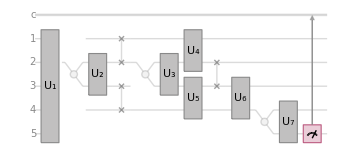
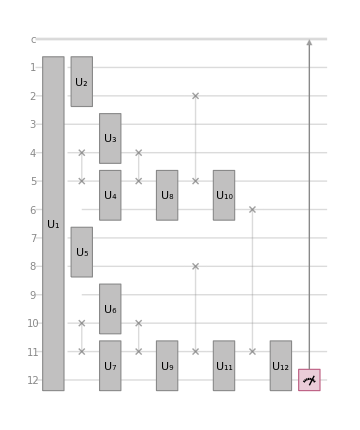
-Graphics-XOR With Copy-Graphics-XOR Without Copy

-Graphics-

```mathematica
Row[{Labeled[circuitPlot[XorFromNandGatesCircuit], "XOR With Copy"],Spacer[50], Labeled[circuitPlot[XorFromNandGatesCircuitNoCopy], "XOR Without Copy"]}]
```

```mathematica
Export["C:\\Users\\chris\\Documents\\WolframAlpha Notebook Edition\\WSRP\\Universal Set of Quantum Gates\\Pictures\\circuit2.png", %]
```

C:\Users\chris\Documents\WolframAlpha Notebook Edition\WSRP\Universal Set of Quantum Gates\Pictures\circuit2.png

```mathematica
Export["C:\\Users\\chris\\Documents\\WolframAlpha Notebook Edition\\WSRP\\Universal Set of Quantum Gates\\Pictures\\circuit1.png", %]
```

C:\Users\chris\Documents\WolframAlpha Notebook Edition\WSRP\Universal Set of Quantum Gates\Pictures\circuit1.png

Here is a visualization of the matrices for each column of the smaller XOR circuit:
The first and last matrices are not square, because they setup and measure the state vector, respectively.
The interior gate matrices are mostly diagonally-shaped, because they are composed of only one gate matrix, but many identity matrices.

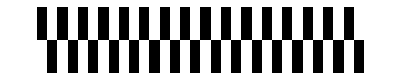
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot /@ circuitMatrices[XorFromNandGatesCircuit]
```

Here is the composition of all of the interior matrices:

```mathematica
circuitMatrix[XorFromNandGatesCircuit[[2;;-2]]]//ArrayPlot
```

-Graphics-

And here is the final composition of all the matrices, which makes a matrix representation of XOR:

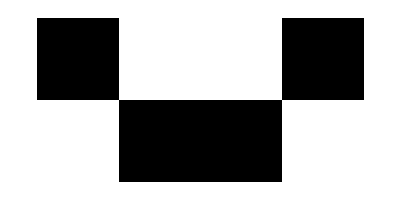

-Graphics-

```mathematica
circuitMatrix[XorFromNandGatesCircuit]//ArrayPlot
```

```mathematica
-Graphics-
-Graphics-
```

-Graphics-

-Graphics-

```mathematica
Export["C:\\Users\\chris\\Downloads\\thinginfininifen3.png", %]
```

C:\Users\chris\Downloads\thinginfininifen3.png

## Universal Gates

### Definition

A set of universal gates can be formulated as the set of gates that comprises matrix decompositions to all other possible gates.

#### Classical Definition

A set of gates is universal if, for all possible 2x2 gates T, there exists an equivalent circuit with some number of wires w and some number of gates m such that the columns c_i of the circuit apply a gate to wires λ_1 through λ_2. Formally,
S_g is a set of universal gates iff ∀G∈S_G,∀G_I∈G,G_i∈{e_1, e_2, e_3, e_4} of 𝔹^4,∀{T∈𝔹^(4×4)|∀T_i∈T,T_i∈{e_1, e_2, e_3, e_4} of 𝔹^4}∃w∈ℕ, m∈ℕ|(P∈𝔹^(2^w×4)|∀P_i∈P,P_i∈{e_1, e_2, e_3, e_4}of 𝔹^4 )×((c_1×c_2... c_m)|c_i∈{I_2^(⊗λ_1)⊗G⊗I_2^(⊗λ_2)∀λ_1∈ℕ, λ_2∈ℕ|G∈S_G∧λ_1+2+λ_2==w}))×(R∈𝔹^(4×2^w)|∀R_i∈R,R_i∈{e_1, e_2, e_3, e_4} of 𝔹^4)==T,
where P and R are state preparation and reduction matrices, respectively.

#### Quantum Definition

Very similar to the classical definition, but with a few requirements for quantum gates and the possibility of complex unit vectors. Thus,
S_g is a set of quantum universal gates iff ∀G∈S_G,G is unitary∧∀G_i∈G,||G_i||==1},∀{T∈ℂ^(4×4)|T is unitary∧∀T_i∈T,||T_i||==1}∃w∈ℕ, m∈ℕ|(P∈𝔹^(2^w×4)|∀P_i∈P,P_i∈{e_1, e_2, e_3, e_4} of 𝔹^4)×((c_1×c_2... c_m)|c_i∈{I_2^(⊗λ_1)⊗G⊗I_2^(⊗λ_2)∀λ_1∈ℕ, λ_2∈ℕ|G∈S_G∧λ_1+2+λ_2==w}))×(R∈𝔹^(4×2^w)|∀R_i∈R,R_i∈{e_1, e_2, e_3, e_4}of 𝔹^4 )==T,
where P and R are state preparation and reduction matrices, respectively.

## Classical Universality

### Classical 2→1 Universality Proof

#### Theorem

A gate set containing at least one gate that satisfies each of the following properties is universal:

G(a, a) = ¬a

G(0, 0) + G(0, 1) + G(1, 0) + G(1, 1) is Odd

#### Lemma 1:

In order to make a 2→1 NOT gate, a gate set must have a gate which satisfies the property G(a, a) = ¬a.

In order for a gate to be universal, it needs to be able to implement any 2-bit gate, including the 2-bit NOT gates: (0 | 1 | 0 | 1
1 | 0 | 1 | 0) or (0 | 0 | 1 | 1
1 | 1 | 0 | 0). The 2-bit NOT gates comprise a 1-bit NOT gate on a single wire, and a 1-bit NOT gate can be constructed by using only that single bit of the 2-bit version. Thus, the ability of a gate set to construct a 2-bit NOT gate is equivalent to it’s ability to construct a 1-bit NOT gate.
The only way for a 1-bit NOT gate to be constructed from a 2→1 gate is if the gate satisfies the property that G(a, a) = ¬a, because the input wire to the gate can be duplicated, thus constructing a NOT gate.

#### Lemma 2:

For 2→1 gates with two 1-valued outputs, the number of 1-valued outputs stays the same under NOT transformations.

Define the sum of a gate to be the parity of the sum of the digits in it’s truth table. I.e., the number of 1-valued outputs.
The truth table of a gate constructed from applying a NOT gate to it’s first wire then applying some other 2→1 gate is equivalent to the truth table of the other gate mirrored horizontally. The same is true for NOT gates applied to the second input being equivalent to a vertical mirroring of the original truth table. Moving the values of a truth table does not change the sum, so these transformations of a gate preserve sum.
For a gate constructed by applying a NOT gate to the output of some other gate, because all the outputs of 0 will turn to 1, and there are 4-n 0s in the truth table for a gate with n 1s, then the sum of the new gate will be 4 - (sum of the old gate).
For gates with a sum of 2, the value thus never changes under transformations of NOT.

#### Corollary to Lemma 2:

2→1 gates with a sum of 2 can be decomposed into 1-bit NOT gates.

The identity truth table represents a gate which has no effect on the wires of the circuit. Because the identity gate has a sum of 2, this means that it is equivalent to all other gates with a sum of 2 under NOT gate transformations.
As identity gates can be removed with no effect to the circuit, any 2-sum gate is equivalent to some transformation of 1-bit not gates. If a gate set already has the ability to implement NOT gates, which every universal set must by Lemma 1, then 2-sum gates are always decomposable into other gates of the set.

#### Proof:

By Lemma 1, all universal gate sets must have a gate with the property G(a, a) = ¬a.
By the Corollary to Lemma 2 gates with 2-sum are decomposable to NOT, and because the only other even-sum gates have a constant output, a universal gate set must contain a gate with odd parity.

#### Results:

Out of all of the possible 2→1 gates

```mathematica
truthTable[BooleanFunction[#, 2], "func"<>ToString[#]]&/@Range[0, 15]
```

{func0 | 0 | 1
0 | 0 | 0
1 | 0 | 0,func1 | 0 | 1
0 | 1 | 0
1 | 0 | 0,func2 | 0 | 1
0 | 0 | 1
1 | 0 | 0,func3 | 0 | 1
0 | 1 | 1
1 | 0 | 0,func4 | 0 | 1
0 | 0 | 0
1 | 1 | 0,func5 | 0 | 1
0 | 1 | 0
1 | 1 | 0,func6 | 0 | 1
0 | 0 | 1
1 | 1 | 0,func7 | 0 | 1
0 | 1 | 1
1 | 1 | 0,func8 | 0 | 1
0 | 0 | 0
1 | 0 | 1,func9 | 0 | 1
0 | 1 | 0
1 | 0 | 1,func10 | 0 | 1
0 | 0 | 1
1 | 0 | 1,func11 | 0 | 1
0 | 1 | 1
1 | 0 | 1,func12 | 0 | 1
0 | 0 | 0
1 | 1 | 1,func13 | 0 | 1
0 | 1 | 0
1 | 1 | 1,func14 | 0 | 1
0 | 0 | 1
1 | 1 | 1,func15 | 0 | 1
0 | 1 | 1
1 | 1 | 1}

there exist only two gates which individually satisfy both of the properties given above:

```mathematica
truthTable[BooleanFunction[#, 2], "func"<>ToString[#]]&/@{7, 14}
```

{func7 | 0 | 1
0 | 1 | 1
1 | 1 | 0,func14 | 0 | 1
0 | 0 | 1
1 | 1 | 1}

Thus, these two gates, the NAND and NOR, respectively, are the only two gates which are individually universal.

### Classical 2→2 Universality Proof

#### Theorem:

Any 2→1 universal gate set can be made into a 2→2 universal gate set.

#### Lemma 1:

All 2→2 gates can be decomposed into two 2→1 gates (G_α(x, y), G_β(x, y)).

#### Lemma 2:

Any of the following forms allow a 2→1 gate to be constructed by only using a single output bit of a 2→2 gate:

(G(x, y), 0)
(G(x, y), 1)
(0,G(x, y))
(1, G(x, y))
(G(x, y), x)
(G(x, y), y)
(x,G(x, y))
(y,G(x, y))

#### Proof:

Thus, the gates of any 2→1 universal gate set can be transformed into 2→2 gates which themselves are universal to the 2→2 gates.
(Although there are also more ways to construct universal 2→2 gates, such as by combining a universal 2→1 gate set of length two into a single 2→2 gate.)

## Quantum Universality

### Quantum Matrix Definitions

Here are a number of gates that I will use. Most of these are specific or specialized to quantum computing. I will explain most of them throughout the following section.

```mathematica
(* Arbitrary Rotation Gates *)
gateRX[θ_] := ({{Cos[θ/2], -ⅈ Sin[θ/2]}, {-ⅈ Sin[θ/2], Cos[θ/2]}})//N;
gateRY[θ_] := ({{Cos[θ/2], -Sin[θ/2]}, {Sin[θ/2], Cos[θ/2]}})//N;
gateRZ[θ_] := ({{1, 0}, {0, Cos[θ]+ⅈ Sin[θ]}})//N;

(* Other Rotation Gates *)
gateX = ({{0, 1}, {1, 0}})//N;  (* Equivalent to gateRX[π] *)

gateT = ({{1, 0}, {0, 1/(√2)+ⅈ/(√2)}})//N;  (* Equivalent to gateRZ[π/2] *)

gateSqrtY = gateRY[Pi/2];  (* Equivalent to gateRY[π/2] *)
gateSqrtX = gateRX[Pi/2];

(* Other Gate Types *)
gateH = 1/(√2)({{1, 1}, {1, -1}})//N;
gateS = ({{1, 0}, {0, ⅈ}})//N;

(* Controlled Gates *)
gateCNOT = ({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});
gateCZ[θ_]:= ({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, Cos[θ]+ⅈ Sin[θ]}})

(* 2×2 SWAP Gate *)
gateSWAP=({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}});
```

### Single Qubit Gates

#### Bloch Sphere Implementation

This is the code for a visualization of a Bloch Sphere, which is a representation of a single qubit’s quantum state.

```mathematica
BlochSphere[state_] := Module[{θ, φ},
  (* Calculate angles θ and φ from the state vector *)
  θ = 2 ArcCos[Abs[state[[1]]]];
  φ = Arg[state[[2]]];
  {Sin[θ] Cos[φ], Sin[θ] Sin[φ], Cos[θ]}
]

qubitStateGraphics[s_, imSize_:Large, labels_:True]:=
 Graphics3D[{
   (* Draw Transparent Bloch Sphere *)
   Opacity[0.4],
   Sphere[{0, 0, 0},1],
   Opacity[1],
   
   (* Axes and Labels *)
   Black,
   Arrow[{{0, 0, 0},{1.3, 0, 0}}], Text["X Axis", {1.5, 0, 0}],
   Arrow[{{0, 0, 0},{0, 1.3, 0}}], Text["Y Axis", {0, 1.5, 0}],
   Arrow[{{0, 0, 0},{0, 0, 1.3}}], Text["Z Axis", {0, 0, 1.5}],
   
   (* Display State Vector *)
   Red,
   Arrow[{{0, 0, 0},1.3*BlochSphere[s]}],
   If[labels, Text[ToString[N[s]], 1.5*BlochSphere[s]]]
   },
  
  (* Options *)
  PreserveImageOptions->False,
  ViewVector->{10, 7, 5},
  Boxed->False,
  ImageSize->imSize,
  PlotRange->1.5*{{-1, 1}, {-1, 1}, {-1, 1}}
 ]

singleQubitGatesGraphics[g_, imSize_:Large, i0_:0]:=
 Manipulate[Module[{state, M},
  (* Generate State from Gates *)
  M=Dot@@Reverse@g[[1;;i]];
  state=M.{1, 0};
  qubitStateGraphics[state, imSize]
 ],
 {i, i0, Length[g], 1}
]
```

#### Bloch Sphere Visualization

A Bloch Sphere is a visualization of a qubit state α|0⟩+β|1⟩, where α, β ∈ ℂ^2 such that (|α|)^2+(|β|)^2=1. Although a space of two complex numbers is isomorphic to ℝ^4, not ℝ^3, the global phase of a state (i.e., the imaginary component of α) has no physical significance, and can be discarded, leaving only three dimensions necessary to be visualized.
The state vector projected onto the Z-axis corresponds to the qubit’s probability of being measured 0 or 1 (technically, the Z-projection gives the square root of probability), and the rotation about the Z-axis corresponds to the relative phase between the |0⟩ and |1⟩ states.

For example, here is a Bloch sphere visualizing a rotation of π/3 about the Y-axis:

```mathematica
θ={0, Pi/5, 2 Pi/5, 3 Pi/5, 4 Pi/5, Pi};
Row[qubitStateGraphics[{1,0}.RotationMatrix[-0.5#], Small, False]&/@θ]
```

-Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D-

#### Arbitrary Rotation Gates

The most common quantum computing gates correspond to rotations around the principal axes.

The arbitrary rotation gates are R_x(θ), R_y(θ), R_z(θ),
and the rotations with θ=π are denoted X, Y, and Z,
and the rotations with θ=π/2 are denoted X^(1/2), Y^(1/2), Z^(1/2).

In order for a gate set to be universal, it must be able to reach any point on the sphere, because the gates R_x(θ),R_z(φ) are able to reach any point in spherical coordinates (1, θ, φ).
This presents a problem, as any arbitrary rotation gate R_u(θ) is technically an infinite set of gates for all choices of θ. This can be solved by only approximating arbitrary rotations with a smaller, finite set of rotations.

```mathematica
Labeled[Show@@(qubitStateGraphics[{1,0}.RotationMatrix[-#], Large, False]&/@Range[0, 2Pi, Pi/50]), "Approximating arbitrary Y-rotation \nwith a finite number of gates"]
```

-Graphics3D-Approximating arbitrary Y-rotation 
with a finite number of gates

By the Solovay-Kitaev theorem, an arbitrary rotation to within an accuracy of ε can be done efficiently in O(log^k(1/ε)) complexity for some number k. However, this approach may use multiple types of gates, and so may not give the minimal number of gates possible.
Instead, I developed my own algorithm for implementing arbitrary rotations by using a π/4 rotation about one axis, and a rotation of at most φ=√2×ε in a perpendicular axis.
(The φ=√2×ε comes from finding the nearest multiple of φ to an arbitrary angle θ. The angular distance is at most 1/2 φ in 2D and (√2)/2 φ in 3D, in the case where θ is directly in between the multiples of φ. As ε goes to zero, because we are working on the unit sphere, the euclidian distance approaches the angular distance in radians. Until then, the maximum euclidian distance is less than the maximum angular distance. In the original definition, ε was defined in terms of the max euclidian distance of the columns, so using the formula  (√2)/2 φ<=ε, we get that φ=√2×ε.)

#### In-Depth Solution Example

For example, every arbitrary rotation can be applied with a Y^(1/2)=R_y(π/2) and a small R_z(φ) gate with such a method:
In order to implement R_z(θ), one must apply the R_z(φ) gate θ/φ  times.

```mathematica
φRotation = 0.01;
θRotation = Pi/3;
a=AnimationVideo[
 qubitStateGraphics[{1, 0} . gateH . (gateRZ[φRotation]^i), Large, False],
 {i, 1, ⌊θRotation/φRotation⌋, 1}]
Save["RZRotation", a]
```

AnimationVideo::prpchg: Warning: the output frame rate changed from 104/5 to 10000000/480769.

In order to implement R_x(θ), one must apply the R_z(θ) gate, then the Y^(1/2) gate, which maps the Z-axis rotation to an X-axis rotation.

```mathematica
φRotation=0.01;
θRotation=Pi/3;
i=⌊θRotation/φRotation⌋
a=AnimationVideo[
qubitStateGraphics[{1,0}.gateH.(gateRZ[φRotation]^i).gateRY[Yθ], Large, False],
{Yθ, 0, Pi/4}]
Save["C:\\Users\\chris\\Documents\\WolframAlpha Notebook Edition\\WSRP\\Universal Set of Quantum Gates\\RYRotation.GIF", a]
```

104

In order to implement R_y(θ), one must apply R_x(-θ), then the Z^(1/2) gate, which maps the X-axis rotation to a Y-axis rotation.

```mathematica
φRotation=0.01;
θRotation=Pi/3;
i=⌊θRotation/φRotation⌋
Yθ=Pi/4
a=AnimationVideo[
qubitStateGraphics[
{1,0}.gateH.(gateRZ[-φRotation]^i).gateRY[Yθ].gateRZ[Zθ],Large, False],
{Zθ, 0, Pi/4}]
Save["RZRotation", a]
```

104

π/4

A more accurate visualization can be seen at this link, where the |+⟩ state is rotated around the Z, X, and Y axes with only the R_z gate: https://algassert.com/quirk#circuit={%22cols%22:[[%22Y^%C2%BD%22,%22Y^%C2%BD%22,%22Y^%C2%BD%22],[%22Bloch%22,%22Bloch%22,%22Bloch%22],[1,%22%E2%80%A6%22],[%22Z^t%22,%22Z^t%22,%22Z^t%22],[%22Bloch%22,%22Bloch%22,%22Bloch%22],[1,%22Y^%C2%BD%22,%22Y^%C2%BD%22],[1,%22Bloch%22,%22Bloch%22],[1,1,{%22id%22:%22Z^ft%22,%22arg%22:%221/2%22}],[1,1,%22Bloch%22],[1,%22%E2%80%A6%22],[%22Bloch%22,%22Bloch%22,%22Bloch%22]]}

#### Single-Qubit Gates

All single-qubit gates can be implemented with these simple rotations, so these two gates of Y^(1/2) and R_z(φ) make a universal set for single-bit gates. However, because they are both 1→1 gates, they cannot make different wires interact, and so are not themselves universal for 2→2 gates.

### Multi-Qubit Gates

The simplest way to make a universal set of 2→2 gates from a universal set of 1→1 gates is to add on the CNOT gate. The CNOT, or controlled not, applies a π/2 flip in the X axis--equivalent to a bit flip in classical computing--only when the control qubit is in the one state. This allows two qubits to be entangled together very easily, such as in the following circuit:

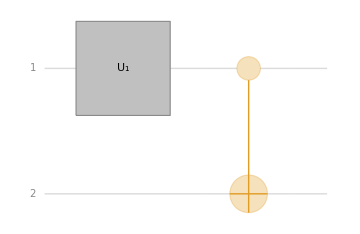

```mathematica
circuitPlot[{{{1, 1}, gateH}, {{1, 2}, gateCNOT}},Medium]
```

Which will transfer the state |ψ⟩|0⟩ to |ψψ⟩. Whenever you measure the first qubit in the X-basis, you will know the value of the second qubit in the X-basis.

In order to make my gate set universal, I need to implement some type of controlled operation. I could add CNOT, which would make it universal, or I can replace my R_z(φ) with a controlled arbitrary rotation CR_z(φ).

### Proof of Universality

Now that a multi-qubit gate has been added, it is possible to prove that my gate set of {Y^(1/2), CR_z(φ)} is universal.
I will use R_z(θ) instead of R_z(φ) (i.e., the arbitrary controlled gate instead of my discretized approximation) because it makes the circuits much more accurate and simple. It is possible to implement this all with R_z(φ), but infeasible, and they are equivalent to within an error of ε.

#### Other Universal Sets

There are a variety of universal quantum gates that have already been found. Some of these, such as {Toffoli, H} or {CCiR_x(aπ) for an irrational a} use very few gates, but require 3→3 qubit gates (i.e., the Toffoli and CCiR_x), but the starting point for my formulation will rely on the universal set {H, S, CNOT, T}.
These four gates are a universal set, so if any set of gates that can create H, S, CNOT, and T, then it is also universal.

#### Proof of CNOT

This gate applies the CNOT using only gates from my universal set. The way it works is by transforming a controlled Z rotation into a controlled X rotation by rotating it with the Y^(1/2) gate:

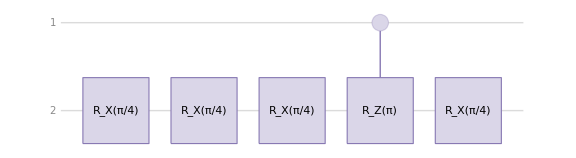

```mathematica
proofOfCNOT={
{{2, 2}, gateSqrtX},
{{2, 2}, gateSqrtX},
{{2, 2}, gateSqrtX},
{{1, 2, Pi}, gateCZ},
{{2, 2}, gateSqrtX}
};
circuitPlot[proofOfCNOT, Large]
```

Here are the complex matrices that make up my CNOT gate:

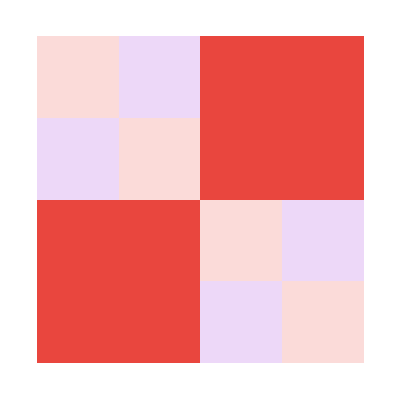
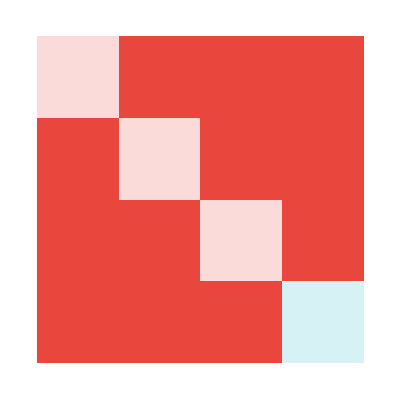
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ComplexArrayPlot/@circuitMatrices[proofOfCNOT]
```

And here is the final result when the matrices are multiplied, compared to the actual CNOT:

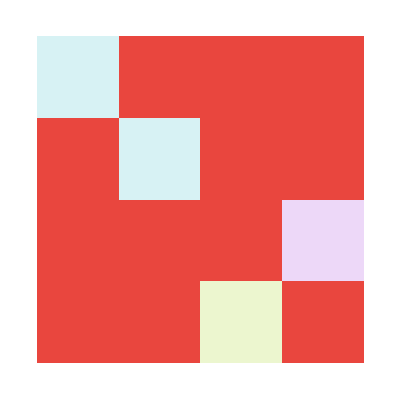
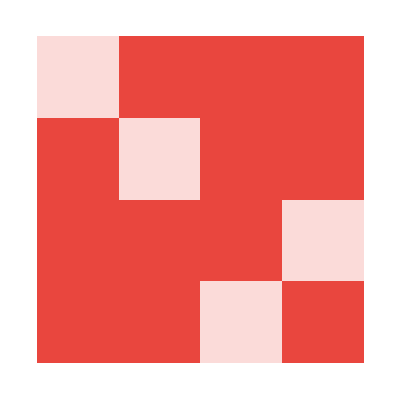

```mathematica
ComplexArrayPlot/@{Round[circuitMatrix[proofOfCNOT], 10^-10], gateCNOT}
```

The reason that they are different colors is because of global phase, because the |00⟩ state has a phase angle of π, so it has a phase coefficient of -1. Global phase can’t be measured or used for computation, so, dividing by this global phase coefficient, it is proven that my CNOT and the conventional CNOT are exactly equal:

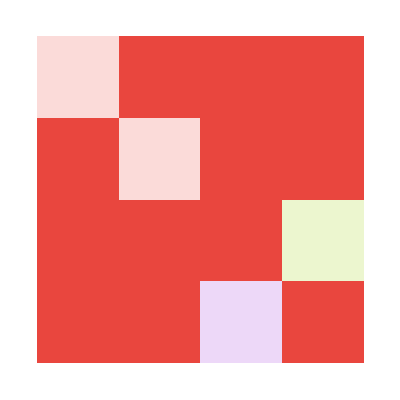
{-Graphics-,-Graphics-}

```mathematica
ComplexArrayPlot/@{-1*Round[circuitMatrix[proofOfCNOT], 10^-10], gateCNOT}
```

#### Proof of T

This gate applies the T using only gates from my universal set. The T gate itself is super simple, because T is equivalent to R_z(π/4). However, R_z and CR_z are considered different gates, so in order to implement a R_z, I first need to use my state preparation to my advantage in order to get a qubit in the |1⟩ state.

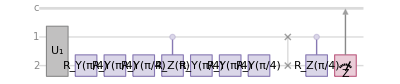

```mathematica
proofOfT={
{{2, 2}, matrixRepeatExpand},

(* First, get |Subscript[ψ, 1]⟩ into the |1⟩ state *)
{{2, 2}, gateSqrtY},
{{2, 2}, gateSqrtY},
{{2, 2}, gateSqrtY},
{{1, 2, Pi}, gateCZ},
{{2, 2}, gateSqrtY},
{{2, 2}, gateSqrtY},
{{2, 2}, gateSqrtY},

(* Apply Rz Gate *)
{{1, 2},gateSWAP},
{{1, 2, Pi / 4},gateCZ},

{{2,2}, matrixReturn}
};
circuitPlot[proofOfT, Full]
```

Here are the complex matrices that make up my T gate:

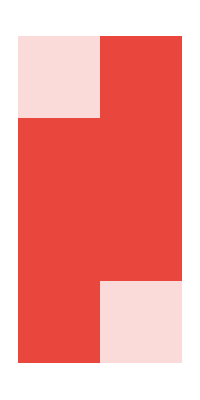
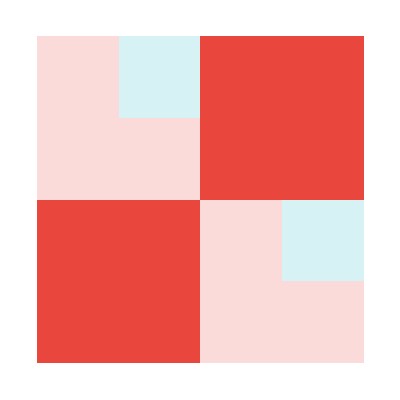
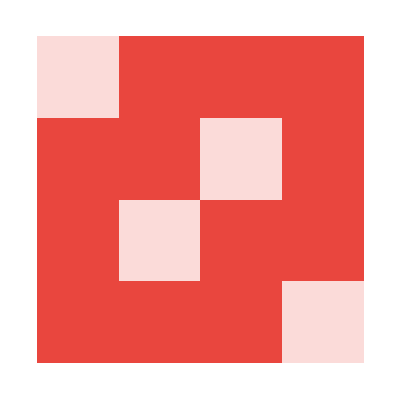
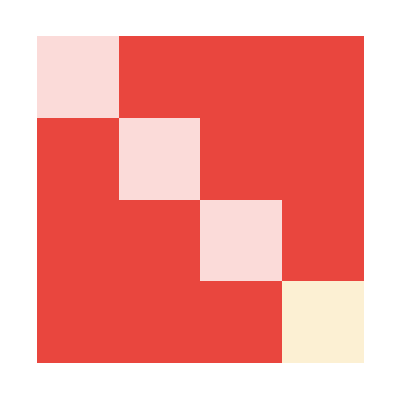
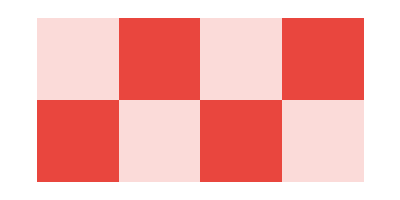
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ComplexArrayPlot/@circuitMatrices[proofOfT]
```

And here is the final result when the matrices are multiplied, compared to the actual H:

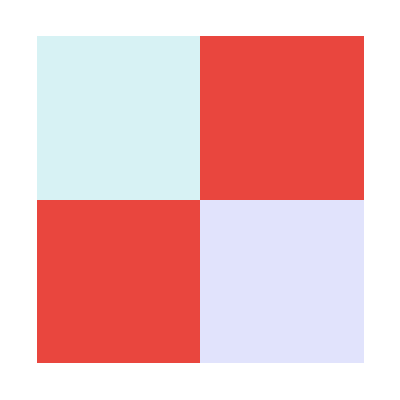
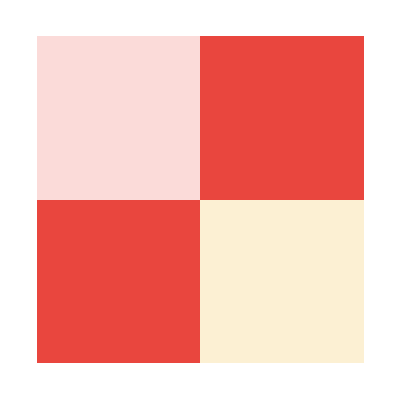

```mathematica
ComplexArrayPlot/@{Round[circuitMatrix[proofOfT], 10^-10], gateT}
```

Again, global phase is messing with the colors. Correcting for that, these matrices are equivalent:

```mathematica
ComplexArrayPlot/@{-1*Round[circuitMatrix[proofOfT], 10^-10], gateT}
```

{-Graphics-,-Graphics-}

#### Proof of S

S is the easiest gate to prove, because it is equivalent to T^2. In order to apply the S gate, one can simply apply two T gates. However, I will also show a full construction of it using the method I’ve used so far.

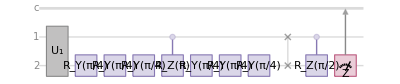

```mathematica
proofOfS={
{{2, 2}, matrixRepeatExpand},

(* First, get |Subscript[ψ, 1]⟩ into the |1⟩ state *)
{{2, 2}, gateSqrtY},
{{2, 2}, gateSqrtY},
{{2, 2}, gateSqrtY},
{{1, 2, Pi}, gateCZ},
{{2, 2}, gateSqrtY},
{{2, 2}, gateSqrtY},
{{2, 2}, gateSqrtY},

(* Apply Rz Gate *)
{{1, 2},gateSWAP},
{{1, 2, Pi / 2},gateCZ},

{{2,2}, matrixReturn}
};
circuitPlot[proofOfS, Full]
```

Here are the complex matrices that make up my S gate:

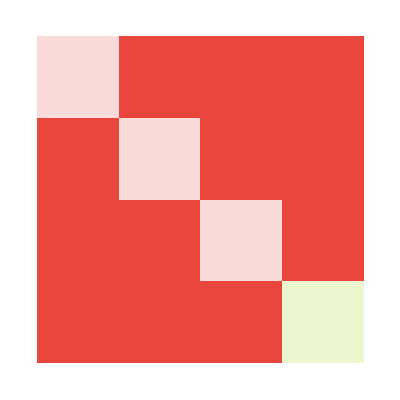
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ComplexArrayPlot/@circuitMatrices[proofOfS]
```

And here is the final result when the matrices are multiplied, compared to the actual H:

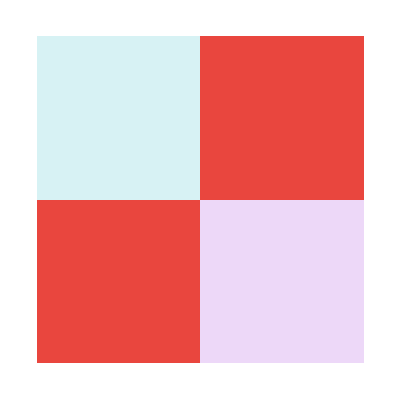
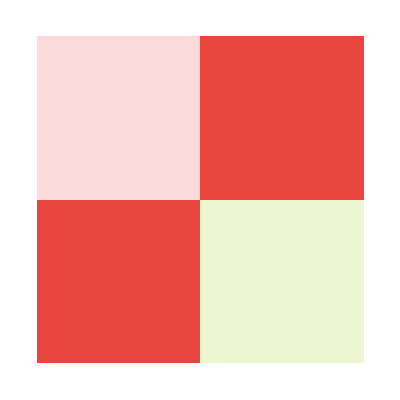

```mathematica
ComplexArrayPlot/@{Round[circuitMatrix[proofOfS], 10^-10], gateS}
```

Again, global phase is messing with the colors. Correcting for that, these matrices are equivalent:

```mathematica
ComplexArrayPlot/@{-1*Round[circuitMatrix[proofOfS], 10^-10], gateS}
```

{-Graphics-,-Graphics-}

#### Proof of H

This gate applies the H using only gates from my universal set. Very similar to T and S, it relies on transforming a qubit to the |1⟩ state, then using the controlled z rotation to implement the actual logic.

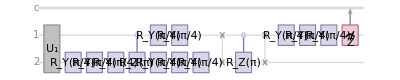

```mathematica
proofOfH={
{{2, 2}, matrixRepeatExpand},

(* First, get |Subscript[ψ, 1]⟩ into the |1⟩ state *)
{{2, 2}, gateSqrtY},
{{2, 2}, gateSqrtY},
{{2, 2}, gateSqrtY},
{{1, 2, Pi}, gateCZ},
{{2, 2}, gateSqrtY},
{{2, 2}, gateSqrtY},
{{2, 2}, gateSqrtY},

(* Apply Rz Gate *)
{{1, 1},gateSqrtY},
{{1, 1},gateSqrtY},
{{1, 2},gateSWAP},
{{1, 2, Pi},gateCZ},
{{1, 2},gateSWAP},
{{1, 1},gateSqrtY},
{{1, 1},gateSqrtY},
{{1, 1},gateSqrtY},


{{1,1}, matrixReturn}
};
circuitPlot[proofOfH, Full]
```

Here are the complex matrices that make up my H gate:

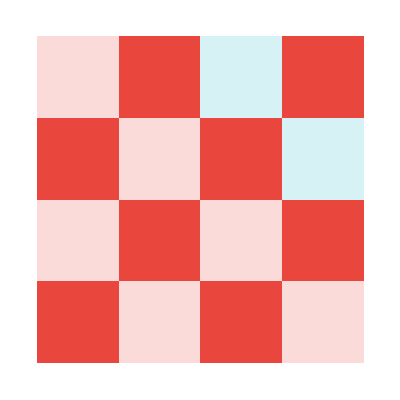
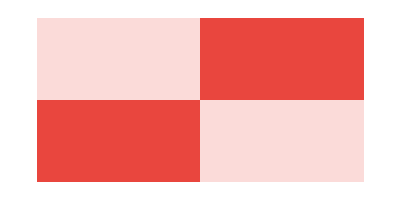
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ComplexArrayPlot/@circuitMatrices[proofOfH]
```

And here is the final result when the matrices are multiplied, compared to the actual H:

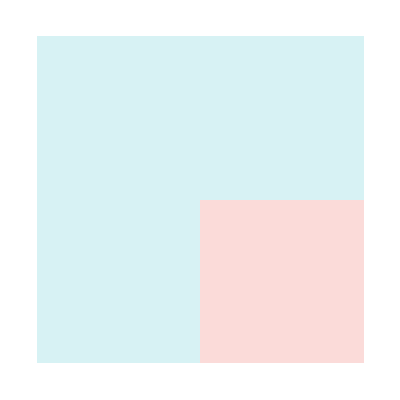
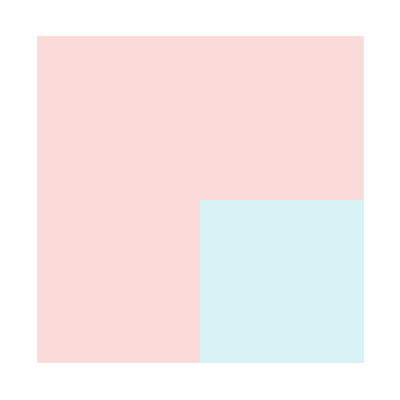

```mathematica
ComplexArrayPlot/@{Round[circuitMatrix[proofOfH], 10^-10], gateH}
```

Again, global phase is messing with the colors. Correcting for that, these matrices are equivalent:

```mathematica
ComplexArrayPlot/@{-1*Round[circuitMatrix[proofOfH], 10^-10], gateH}
```

{-Graphics-,-Graphics-}

#### Note on 1→1 vs 2→2

Changing the Y^(1/2) gate from a 1→1 gate to a 2→2 gate is trivial, as you can just Kronecker product two Y^(1/2) gates together into Y^(1/2)⊗Y^(1/2) and only use a single input and output qubit of each. Just as the ability of a gate set to implement 1→1 NOT is equivalent to it’s ability to implement 2→2 NOT, it follows that the same holds true for any single-qubit gate. This Y^(1/2)⊗Y^(1/2) gate has the following matrix form: (1/2 | -1/2 | -1/2 | 1/2
1/2 | 1/2 | -1/2 | -1/2
1/2 | -1/2 | 1/2 | -1/2
1/2 | 1/2 | 1/2 | 1/2), and can be denoted Y^(1/2⊗2).

#### Results

Omitting the state preparation and copy gates, which are only a product of the original classical formulation of universality, this set of two gates, {Y^(1/2⊗2), CR_z(φ)} is universal for all quantum operations.
To my knowledge, this is the smallest set of 2→2 universal quantum gates found thus far.

```mathematica
□^□
```

□^□

## Future Research

Although I have outlined a single set of universal quantum gates, using this construction, it may be possible to construct other similar sets of gates. The most trivial way of doing this would be to create the set {Y^(1/2⊗2), CR_z(φ')}, where φ'<φ. Another possible method would be to change the types of rotation used, such as the set {X^(1/2⊗2), CR_z(φ)}, or even possibly a set with a different axis of controlled arbitrary rotation. Though it is not included in this computational essay for the sake of brevity, I explored controlling the discrete rotation instead of the arbitrarily small rotation (e.g., the set {CY^(1/2⊗2), R_z(φ)}), and I was not able to prove it’s universality. I don’t believe it is possible, but a formal proof of that fact could also be an area for more research.

```mathematica
Show@@Table[
qubitStateGraphics[gateRY[2θ1].gateRZ[2θ2].{1/Sqrt[2], 1/Sqrt[2]}, Large, False],
{θ1, 0, 2Pi, 0.3}, {θ2, 0, 2Pi, 0.3}]
```

-Graphics3D-

#### Bloch Sphere Implementation

This is the code for a visualization of a Bloch Sphere, which is a representation of a single qubit’s quantum state.

```mathematica
BlochSphere[state_] := Module[{θ, φ},
  (* Calculate angles θ and φ from the state vector *)
  θ = 2 ArcCos[Abs[state[[1]]]];
  φ = Arg[state[[2]]];
  {Sin[θ] Cos[φ], Sin[θ] Sin[φ], Cos[θ]}
]

imSize=Large;
 Graphics3D[Join[{
   (* Draw Transparent Bloch Sphere *)
   Opacity[0.4],
   Sphere[{0, 0, 0},1],
   Opacity[1],
   
   (* Axes and Labels *)
   Black,
   Arrow[{{0, 0, 0},{1.3, 0, 0}}], Text["X Axis", {1.5, 0, 0}],
   Arrow[{{0, 0, 0},{0, 1.3, 0}}], Text["Y Axis", {0, 1.5, 0}],
   Arrow[{{0, 0, 0},{0, 0, 1.3}}], Text["Z Axis", {0, 0, 1.5}],
   
   (* Display State Vector *)
   Red},
Table[Arrow[{{0, 0, 0}, 1.3*BlochSphere[gateRZ[2θ3].gateRY[2θ1].gateRZ[2θ2].{1/Sqrt[2], 1/Sqrt[2]}]}],
{θ1, 0, 2Pi, 0.1}, {θ2, 0, 2Pi, Pi/2}, {θ3, 0, 2Pi, 0.1}]],
  
  (* Options *)
  PreserveImageOptions->False,
  ViewVector->{10, 7, 5},
  Boxed->False,
  ImageSize->imSize,
  PlotRange->2*{{-1, 1}, {-1, 1}, {-1, 1}}
 ]
```

-Graphics3D-

```mathematica
BlochSphere[state_] := Module[{θ, φ},
  (* Calculate angles θ and φ from the state vector *)
  θ = 2 ArcCos[Abs[state[[1]]]];
  φ = Arg[state[[2]]];
  {Sin[θ] Cos[φ], Sin[θ] Sin[φ], Cos[θ]}
]

imSize=Large;
 Graphics3D[Join[
{Red},
Table[Arrow[{{0, 0, 0}, 1.3*BlochSphere[gateRY[0.5θ1].{1/Sqrt[2], 1/Sqrt[2]}]}],
{θ1, 0, 6Pi, Pi/12}],

(*{Blue},
Table[Arrow[{{0, 0, 0}, 1.3*BlochSphere[gateRZ[0.5θ1].{1/Sqrt[2], 1/Sqrt[2]}]}],
{θ1, 0, 6Pi, Pi/12}],*)


{
   (* Draw Transparent Bloch Sphere *)
   Opacity[1],
	White,
   Sphere[{0, 0, 0},1],
   Opacity[1],
   
   (* Axes and Labels *)
   Black,
   Arrow[{{0, 0, 0},{1.7, 0, 0}}], Text["X Axis", {1.9, 0, 0}],
   Arrow[{{0, 0, 0},{0, 1.4, 0}}], Text["Y Axis", {0, 1.6, 0}],
   Arrow[{{0, 0, 0},{0, 0, 1.6}}], Text["Z Axis", {0, 0, 1.7}],
   
   (* Display State Vector *)
   }


],
  
  (* Options *)
  PreserveImageOptions->False,
  ViewVector->10{10, 7, 5},
  Boxed->False,
  ImageSize->imSize,
  PlotRange->2*{{-1, 1}, {-1, 1}, {-1, 1}}
 ]
```

-Graphics3D-

```mathematica
Export["C:\\Users\\chris\\Documents\\WolframAlpha Notebook Edition\\WSRP\\Universal Set of Quantum Gates\\Pictures\\TEST.png", %]
```

C:\Users\chris\Documents\WolframAlpha Notebook Edition\WSRP\Universal Set of Quantum Gates\Pictures\TEST.png

```mathematica
Show@@(qubitStateGraphics[{1,0}.RotationMatrix[-#], Large, False]& /@ Range[0, 2Pi, Pi/50])
```

-Graphics3D-

{Y^(1/2⊗2), CR_z(φ)}